```mathematica
"sfg=479nm"
"vis=532nm"
"ir=4820nm(2075cm^-1)"
```

```mathematica
Subscript[β, sfg]=Subscript[Β, sfg] °
Subscript[β, vis]=Subscript[Β, vis] °
Subscript[β, ir]=Subscript[Β, ir] °
Subscript[γ, sfg]=Subscript[Γ, sfg] °
Subscript[γ, vis]=Subscript[Γ, vis] °
Subscript[γ, ir]=Subscript[Γ, ir] °
```

° Β_sfg

° Β_vis

° Β_ir

° Γ_sfg

° Γ_vis

° Γ_ir

```mathematica
"Refractive index -Air/Si-H/Si"
```

```mathematica
Subscript[n, 1,sfg]=Subscript[n, 1,vis]=Subscript[n, 1,ir]=1
```

1

```mathematica
Subscript[n, 2,sfg]=Re[√((4.416+ⅈ×0.033)×(4.416-ⅈ×0.033))]
Subscript[n, 2,vis]=Re[√((4.150+ⅈ×0.033)×(4.150-ⅈ×0.033))]
Subscript[n, 2,ir]=3.423
```

4.41612

4.15013

3.423

```mathematica
Subscript[n, m,sfg]=√(Subscript[n, 2,sfg]-Subscript[n, 1,sfg])
Subscript[n, m,vis]=√(Subscript[n, 2,vis]-Subscript[n, 1,vis])
Subscript[n, m,ir]=√(Subscript[n, 2,ir]-Subscript[n, 1,ir])
```

1.84828

1.77486

1.5566

```mathematica
"Conservation of Momentum -532nm(65.5°)/2075cm^-1/471nm"
```

```mathematica
Subscript[Β, ir]=76
```

76

```mathematica
Subscript[Β, vis]=65.5
Subscript[ω, vis]=18797
Subscript[ω, ir]=2075
```

65.5

18797

2075

```mathematica
Subscript[ω, sfg]=Subscript[ω, vis]+Subscript[ω, ir]
```

20872

```mathematica
Subscript[Β, sfg]=ArcSin[(Subscript[ω, vis] Sin[Subscript[β, vis]]+Subscript[ω, ir] Sin[Subscript[β, ir]])/Subscript[ω, sfg]]/°
```

66.3424

```mathematica
"Snell's Law"
```

```mathematica
Subscript[γ, sfg]=ArcSin[(Sin[Subscript[β, sfg]] Subscript[n, 1,sfg])/Subscript[n, 2,sfg]]
Subscript[γ, vis]=ArcSin[(Sin[Subscript[β, vis]] Subscript[n, 1,vis])/Subscript[n, 2,vis]]
Subscript[γ, ir]=ArcSin[(Sin[Subscript[β, ir]] Subscript[n, 1,ir])/Subscript[n, 2,ir]]
```

0.208929

0.221057

0.287404

```mathematica
"Fresnel Factors"
```

```mathematica
Subscript[L, xx,sfg]= (Subscript[n, 1,sfg] 2 Cos[Subscript[γ, sfg]])/(Subscript[n, 1,sfg] Cos[Subscript[γ, sfg]] + Subscript[n, 2,sfg] Cos[Subscript[β, sfg]])Cos[Subscript[β, sfg]]
Subscript[L, xx,vis]= (Subscript[n, 1,vis] 2 Cos[Subscript[γ, vis]])/(Subscript[n, 1,vis] Cos[Subscript[γ, vis]] + Subscript[n, 2,vis] Cos[Subscript[β, vis]])Cos[Subscript[β, vis]]
Subscript[L, xx,ir]= (Subscript[n, 1,ir] 2 Cos[Subscript[γ, ir]])/(Subscript[n, 1,ir] Cos[Subscript[γ, ir]] + Subscript[n, 2,ir] Cos[Subscript[β, ir]])Cos[Subscript[β, ir]]

Subscript[L, yy,sfg]= (Subscript[n, 1,sfg] 2 Cos[Subscript[β, sfg]])/(Subscript[n, 1,sfg] Cos[Subscript[β, sfg]] +Subscript[n, 2,sfg] Cos[Subscript[γ, sfg]])
Subscript[L, yy,vis]= (Subscript[n, 1,vis] 2 Cos[Subscript[β, vis]])/(Subscript[n, 1,vis] Cos[Subscript[β, vis]] +Subscript[n, 2,vis] Cos[Subscript[γ, vis]])
Subscript[L, yy,ir]= (Subscript[n, 1,ir] 2 Cos[Subscript[β, ir]])/(Subscript[n, 1,ir] Cos[Subscript[β, ir]] +Subscript[n, 2,ir] Cos[Subscript[γ, ir]])

Subscript[L, zz,sfg]=  (Subscript[n, 2,sfg] 2 Cos[Subscript[β, sfg]])/(Subscript[n, 1,sfg] Cos[Subscript[γ, sfg]] +Subscript[n, 2,sfg] Cos[Subscript[β, sfg]])(Subscript[n, 1,sfg]/Subscript[n, m,sfg])^2 Sin[Subscript[β, sfg]]
Subscript[L, zz,vis]=  (Subscript[n, 2,vis] 2 Cos[Subscript[β, vis]])/(Subscript[n, 1,vis] Cos[Subscript[γ, vis]] +Subscript[n, 2,vis] Cos[Subscript[β, vis]])(Subscript[n, 1,vis]/Subscript[n, m,vis])^2 Sin[Subscript[β, vis]]
Subscript[L, zz,ir]= (Subscript[n, 2,ir] 2 Cos[Subscript[β, ir]])/(Subscript[n, 1,ir] Cos[Subscript[γ, ir]] +Subscript[n, 2,ir] Cos[Subscript[β, ir]])(Subscript[n, 1,ir]/Subscript[n, m,ir])^2 Sin[Subscript[β, ir]]
```

0.285454

0.300072

0.25964

0.169981

0.185801

0.137279

0.345517

0.368706

0.371123

```mathematica
"For SSP"
```

```mathematica
Subscript[L, yy,sfg] Subscript[L, yy,vis] Subscript[L, zz,ir]
```

0.0117211

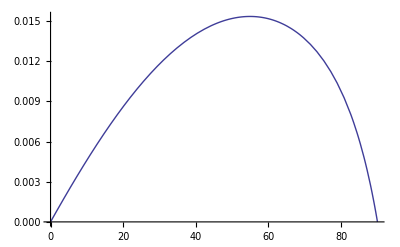

```mathematica
Plot[%,{Subscript[Β, ir],0,90}]
```

```mathematica
"For SPS"
```

```mathematica
Subscript[L, yy,sfg] Subscript[L, zz,vis] Subscript[L, yy,ir]
```

0.00860372

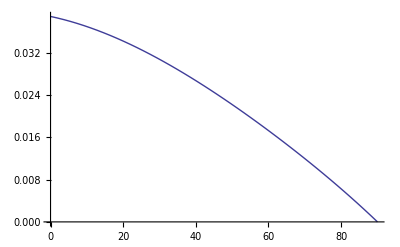

```mathematica
Plot[%,{Subscript[Β, ir],0,90}]
```

```mathematica
"For PSS"
```

```mathematica
Subscript[L, zz,sfg] Subscript[L, yy,vis] Subscript[L, yy,ir]
```

0.00881298

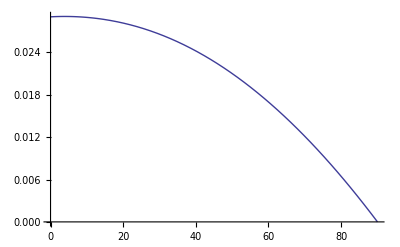

```mathematica
Plot[%,{Subscript[Β, ir],0,90}]
```

```mathematica
"For PPP"
```

```mathematica
-Subscript[L, xx,sfg] Subscript[L, xx,vis] Subscript[L, zz,ir]
-Subscript[L, xx,sfg] Subscript[L, zz,vis] Subscript[L, xx,ir]
Subscript[L, zz,sfg] Subscript[L, xx,vis] Subscript[L, xx,ir]
Subscript[L, zz,sfg] Subscript[L, zz,vis] Subscript[L, zz,ir]
```

-0.0317893

-0.0273268

0.0269195

0.047279

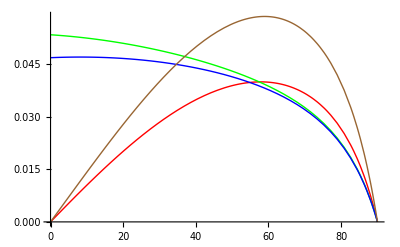

```mathematica
Plot[{-%%%%,-%%%,%%,%},{Subscript[Β, ir],0,90},PlotStyle->{Red,Green,Blue,Brown}]
```